{{32,21.7938},{132,21.7899},{232,21.7813},{332,21.7687},{432,21.7526},17991,{1799632,-68.525},{1799732,-68.5259},{1799832,-68.5269},{1799932,-68.5279}}
 |  |  |  |

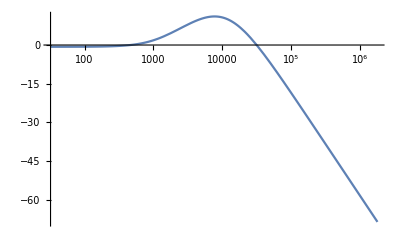

```mathematica
H[f_]=(1+r2a/r1a)*((1/(I *2*π*f*csh2))/(1/(I *2*π*f* csh2)+rsh2))*(rsh1/(rsh1+(1/rpz+1/(1/(I*2*π*f*csh1)))^-1))*((1/rfpre+1/(1/(I*2*π*f*cfpre)))^-1/rin)/.{rin->55310, rsh1->147990, rsh2->148020, csh1->97*10^-12,csh2->130*10^-12, rfpre->681100, cfpre->218*10^-12, rpz->1.5*10^6, r1a->46700, r2a->472500};
a=20*Log10[Sqrt[(ComplexExpand[Re[(H[f])]])^2+(ComplexExpand[Im[(H[f])]])^2]];
list1=Table[{f, a},{f,32, 1.8*10^6,100}];
Export["C:\\Users\\berto\\NotSync\\GitHub\\Laboratorio_3\\Esperienza_03\\Dati\\3_1_teor_a.txt", list1, "Table"];
```